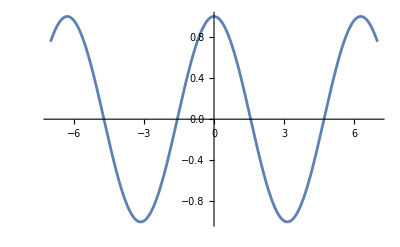
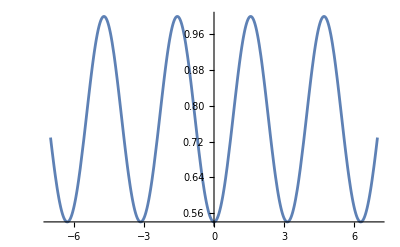
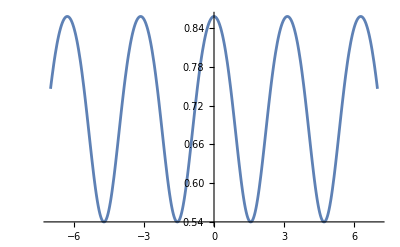
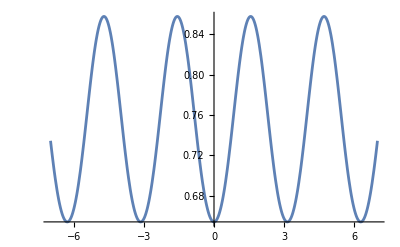
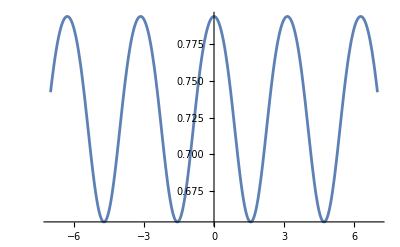

```mathematica
Plot[Nest[Cos, x, #], {x, -7, 7}]&/@Range[1, 5]
```

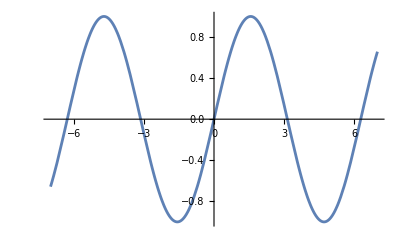
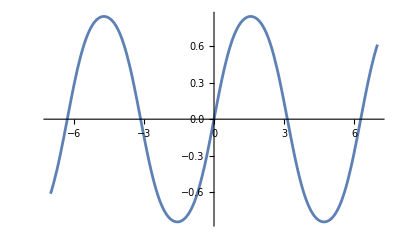
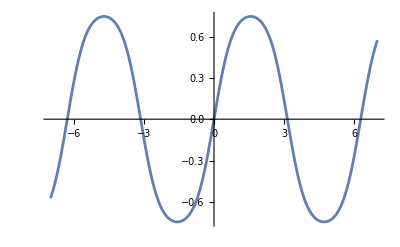
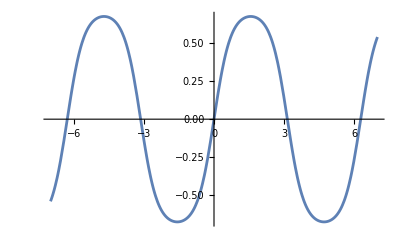
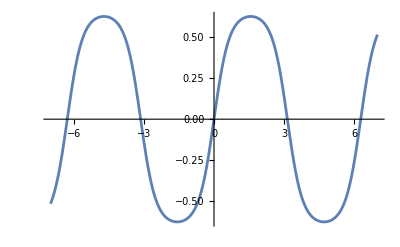

```mathematica
Plot[Nest[Sin, x, #], {x, -7, 7}]&/@Range[1, 5]
```

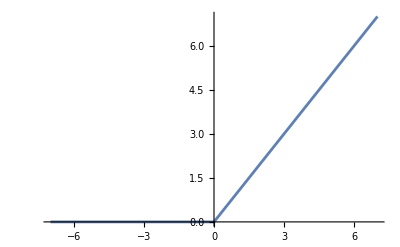
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Plot[Nest[Ramp, x, #], {x, -7, 7}]&/@Range[1, 5]
```

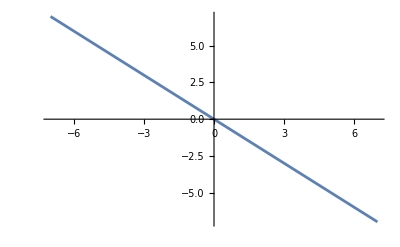
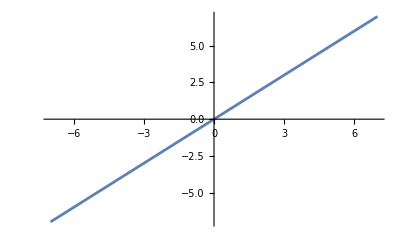
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Plot[Nest[-#&, x, #], {x, -7, 7}]&/@Range[1, 5]
```

```mathematica
LinearSpline[points_][x_]:=Module[{p, m, xs,table},
p=Sort[points,#1[[1]]<#2[[1]]&];
m=If[#1==0,2^16,(#2/#1)]&@@@(Drop[p,1]-Drop[p, -1]);
table=Table[{Drop[p,-1][[i,1]]<=x<Drop[p, 1][[i,1]],m[[i]]*(x-Drop[p,1][[i,1]])+Drop[p,1][[i,2]]},{i,Length[p]-1}];
table=Flatten@Join[{x<p[[1,1]], table[[1,2]]}, table, {x>=p[[-1,1]], table[[-1,2]]}];
Which@@table
]
```

```mathematica
progressMap[func_,l_List, message_:"Complete"]:=Module[{progress=PrintTemporary["0% "<>message]}, Table[NotebookDelete[progress];progress=PrintTemporary[ToString[Round[100*i/Length[l]]]<>"% "<>message]; func[l[[i]]],{i, Length[l]}]]
```

```mathematica
p=RandomReal[{0, 1}, {10, 2}];
r[x_]:=LinearSpline[p][x]
```

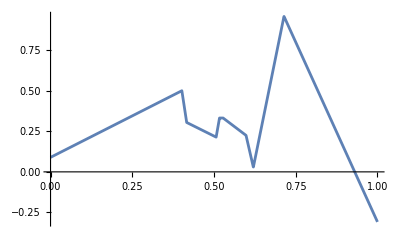
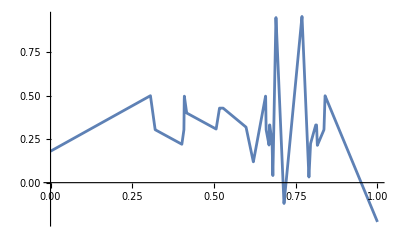
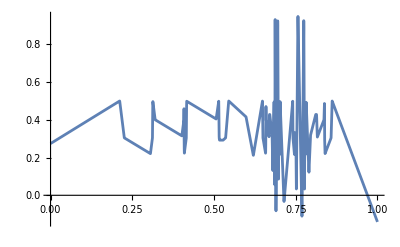
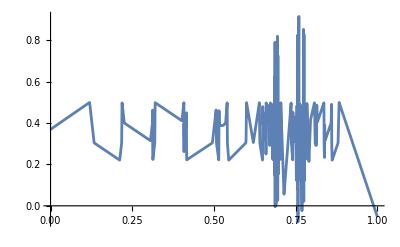
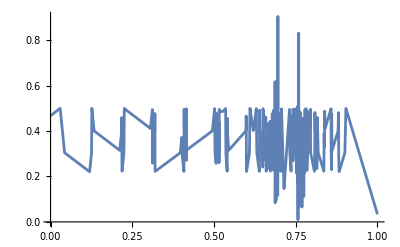
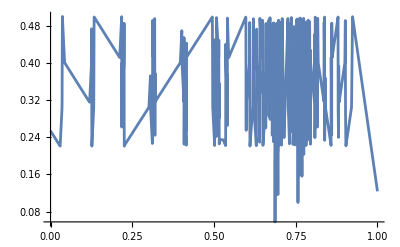
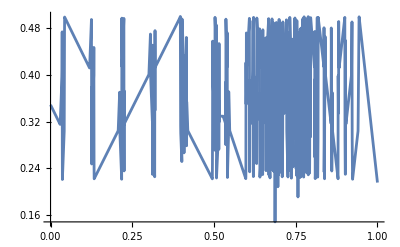
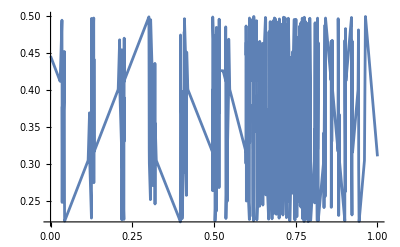

```mathematica
progressMap[Plot[Nest[r, x, #], {x, 0, 1}]&,Range[10]]
```